```mathematica
Get["/home/jadeleon/Documents/quantum_chaotic_channels/Mathematica_packages/QMB.wl"]
```

LeaSpinChainHamiltonian::shdw: Symbol LeaSpinChainHamiltonian appears in multiple contexts {QMB`,Global`}; definitions in context QMB` may shadow or be shadowed by other definitions.

```mathematica
Get["/home/jadeleon/Documents/quantum_chaotic_channels/Mathematica_packages/Chaometer.wl"]
```

Superoperator::shdw: Symbol Superoperator appears in multiple contexts {Chaometer`,Global`}; definitions in context Chaometer` may shadow or be shadowed by other definitions.

```mathematica
L=3;
HamiltonianNN[Jxy_,Jz_,L_]:=
Module[{NNindices},
		NNindices = Normal[ SparseArray[Thread[{#, Mod[# + 1, L, 1]}->1], {L}] &/@ Range[L-1] ];
N[Normal[(1/4)*Total[Join[Jxy*(Pauli/@NNindices),Jxy*(Pauli/@(2NNindices)),Jz*(Pauli[#]&/@(3NNindices))]]]]
	]
```

```mathematica
HamiltonianNN[Jxy,Jz,L]//MatrixForm
```

(0.5 Jz | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.5 Jxy | 0. | 0. | 0. | 0. | 0.
0. | 0.5 Jxy | -0.5 Jz | 0. | 0.5 Jxy | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.5 Jxy | 0. | 0.
0. | 0. | 0.5 Jxy | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.5 Jxy | 0. | -0.5 Jz | 0.5 Jxy | 0.
0. | 0. | 0. | 0. | 0. | 0.5 Jxy | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 Jz)

```mathematica
d=2;
HamiltonianZ[ω_,ϵd_,L_,d_]:=N[(1/2)*(ω*Total[Pauli/@(3*IdentityMatrix[L])]+ϵd*Pauli[Normal[SparseArray[d->3,L]]])]
```

```mathematica
HamiltonianZ[ω,ϵd,L,d]//MatrixForm
```

(0.5 (ϵd+3. ω) | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.5 (ϵd+ω) | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.5 (-1. ϵd+ω) | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.5 (-1. ϵd-1. ω) | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.5 (ϵd+ω) | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.5 (ϵd-1. ω) | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.5 (-1. ϵd-1. ω) | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.5 (-1. ϵd-3. ω))

```mathematica
LeaSpinChainHamiltonian[Jxy_,Jz_,ω_,ϵd_,L_,d_]:=HamiltonianNN[Jxy,Jz,L]+HamiltonianZ[ω,ϵd,L,d]
```

```mathematica
L=3;{#,Mod[# + 1, L, 1]}&/@Range[L-1]
```

{{1,2},{2,3}}

```mathematica
?OpenXXZHamiltonian
```

```mathematica
OpenXXZHamiltonian[3,1,0.2,0.1]
```

{{0.15,-0.05,0.,0.,-0.1,0.,0.,0.},{-0.05,1.15,-1.,0.,0.,-0.1,0.,0.},{0.,-1.,2.15,-0.05,-1.,0.,-0.1,0.},{0.,0.,-0.05,1.15,0.,-1.,0.,-0.1},{-0.1,0.,-1.,0.,1.15,-0.05,0.,0.},{0.,-0.1,0.,-1.,-0.05,2.15,-1.,0.},{0.,0.,-0.1,0.,0.,-1.,1.15,-0.05},{0.,0.,0.,-0.1,0.,0.,-0.05,0.15}}

```mathematica
?ClosedXXZHamiltonian
```

```mathematica
Module[{H},H=ClosedXXZHamiltonian[9,0];{eigenvals,eigenvecs}=Chop[Eigensystem[H]];]
```

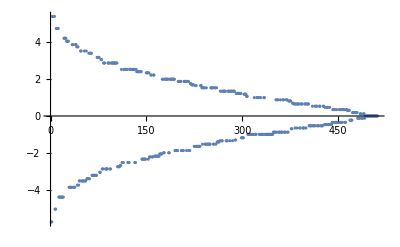

```mathematica
ListPlot[eigenvals]
```

```mathematica
m=ParallelTable[Braket[i,j],{i,eigenvecs},{j,eigenvecs}];
```

```mathematica
DiagonalMatrixQ[m]
```

True

```mathematica
AllTrue[Diagonal[m],#==1&]
```

True

```mathematica
chaometer=4;L=9;
SeedRandom[20349];(*set a seed to always get the same random state ψE *)
ψE={RandomChainProductState[chaometer-1],RandomChainProductState[L-chaometer]};
```

```mathematica
Chop[Superoperator[10.^-2,ψE,eigenvals,eigenvecs,L,chaometer]]
```

{{0.999967,-0.00173237-0.00142174 ⅈ,-0.00173237+0.00142174 ⅈ,0.0000893096},{0.00173255-0.00142178 ⅈ,0.999939+3.08638×10^-8 ⅈ,0.0000139923+0.0000413924 ⅈ,-0.00173236+0.00142184 ⅈ},{0.00173255+0.00142178 ⅈ,0.0000139923-0.0000413924 ⅈ,0.999939-3.08638×10^-8 ⅈ,-0.00173236-0.00142184 ⅈ},{0.0000326278,0.00173237+0.00142174 ⅈ,0.00173237-0.00142174 ⅈ,0.999911}}

```mathematica
L=9;
upspins=5;
downspins=L-upspins;
dim=L!/(upspins! downspins!)
```

792

```mathematica
(*PARAMETERS OF THE HAMILTONIAN*)
Clear[L,upspins,downspins,dim,Jxy,Jz,ϵ,defectsite,alpha,JJxy,JJz];

L=9;
upspins=5;
downspins=L-upspins;
dim=L!/(upspins! downspins!);

(*Impurity*)
ϵ=0.5;
defectsite=Floor[L/2];

(*Parameters for nearest-neighbor couplings*)
Jxy=1.0;
Jz=0.5;

(*Parameters for next-nearest-neighbor couplings*)
(*Set alpha=0 if NNN couplings do not exist*)
alpha=0.0;
JJxy=1.0;
JJz=0.5;

(*BASIS*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];

(*ELEMENTS OF THE HAMILTONIAN*)
(*Impurity and NN couplings*)
Clear[HH];
(*Initialization*)
Do[Do[HH[i,j]=0.,{i,1,dim}],{j,1,dim}];

(*Diagonal elements*)
Do[
(*Impurity*)
If[basis[[i,defectsite]]==1,
HH[i,i]=HH[i,i]+ϵ/2.,HH[i,i]=HH[i,i]-ϵ/2.];
(*Ising interaction*)
Do[If[basis[[i,j]]==basis[[i,j+1]],
HH[i,i]=HH[i,i]+Jz/4.,HH[i,i]=HH[i,i]-Jz/4.];
,{j,1,L-1}];
,{i,1,dim}];

(*Off-diagonal elements*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
howmany=0;
Do[site[kk]=0,{kk,1,L}];
(*Sites where states i and j differ*)
Do[If[basis[[i,k]]!=basis[[j,k]],howmany+=1;site[howmany]=k;];
,{k,1,L}];
(*If only two neighbor sites differ,there is a coupling matrix element*)
If[howmany==2,
If[site[2]-site[1]==1,HH[i,j]=Jxy/2.;HH[j,i]=Jxy/2.;];];
,{j,i+1,dim}];
,{i,1,dim-1}];

(*ELEMENTS OF THE HAMILTONIAN WITH NNN COUPLINGS*)
If[alpha>0,

(*Diagonal elements*)
Do[
(*Ising interaction*)Do[If[basis[[i,j]]==basis[[i,j+2]],
HH[i,i]=HH[i,i]+alpha JJz/4.,HH[i,i]=HH[i,i]-alpha JJz/4.];
,{j,1,L-2}];
,{i,1,dim}];

(*Off-diagonal elements*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
howmany=0;
Do[site[kk]=0,{kk,1,L}];
(*Sites where states i and j differ*)
Do[If[basis[[i,k]]!=basis[[j,k]],howmany+=1;site[howmany]=k;];
,{k,1,L}];
(*If only two next-neighbor sites differ,there is a coupling matrix element*)
If[howmany==2,
If[site[2]-site[1]==2,
HH[i,j]=alpha JJxy/2.;HH[j,i]=alpha JJxy/2.;];];
,{j,i+1,dim}];
,{i,1,dim-1}];

];

(*TOTAL HAMILTONIAN AND DIAGONALIZATION*)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{j,1,dim}],{i,dim}];
Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];
```

```mathematica
Energy//Dimensions
```

{126}

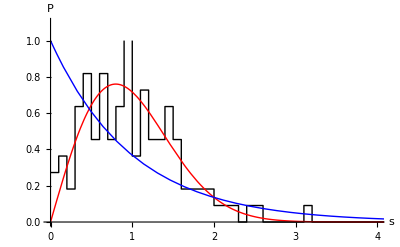

```mathematica
(*LEVEL SPACINGS OF THE UNFOLDED SPECTRUM*)
(*Order the eigenvalues from lowest to highest values*)Clear[Ener];
Ener=Sort[Table[Energy[[k]],{k,1,dim}]];

(*Discard~10% of the eigenvalues located at the borders of the spectrum*)
Clear[percentage,half,spacing];
percentage=0.1 dim;
half=Floor[percentage/2];
Do[Clear[average];
(*Compute the neighboring level spacings for the remaining eigenvalues after unfolding them*)(*Unfolding here means that the average of each group of 10 level spacings=1*)average=(Ener[[half+10 j]]-Ener[[half+10 (j-1)]])/10.;
Do[spacing[i]=(Ener[[half+i]]-Ener[[half-1+i]])/average;,{i,1+10 (j-1),10 j}];,{j,1,Floor[(dim-percentage)/10]}];

(*HISTOGRAM*)
Clear[spcmin,spcmax,bin,Nofbins];
spcmin=0.;
spcmax=8.;
bin=0.1;
Nofbins=IntegerPart[(spcmax-spcmin)/bin];

Clear[SPChist,Nhist];
SPChist[1]=spcmin;
Do[SPChist[i+1]=SPChist[i]+bin,{i,1,Nofbins}];
Do[Nhist[j]=0.,{j,1,Nofbins}];

(*Nhist[j] gives how many spacings we have in the interval SPChist[j+1] and SPChist[j]*)
Do[Do[If[SPChist[j]<spacing[k]<=SPChist[j+1],Nhist[j]=Nhist[j]+1];,{j,1,Nofbins}];,{k,1,10 Floor[(dim-percentage)/10]}];

(*Normalization*)
Clear[Norma];
Norma=Sum[bin Nhist[j],{j,1,Nofbins}];
Do[Nhist[j]=Nhist[j]/Norma,{j,1,Nofbins}];

(*ListPlot with the obtained data*)
Clear[jj,nl];
jj=0;
nl={};
Do[jj+=1;nl=Append[nl,{SPChist[jj],Nhist[jj]}];nl=Append[nl,{SPChist[jj+1],Nhist[jj]}];,{j,1,Nofbins-1}];

DataPlot=ListPlot[nl,Joined->True,PlotRange->{{0,8},{0,1}},PlotStyle->{Black,Thick},LabelStyle->Directive[Black,Bold,Medium],AxesLabel->{"s","P"}];

(*Theoretical curves*)
WignerDyson=Plot[Pi s/2 Exp[-Pi s^2/4],{s,0,8},PlotRange->{0,1},PlotStyle->{Red,Thick},LabelStyle->Directive[Black,Bold,Medium],AxesLabel->{"s","P"}];

Poisson=Plot[Exp[-s],{s,0,8},PlotRange->{0,1},PlotStyle->{Blue,Thick},LabelStyle->Directive[Black,Bold,Medium],AxesLabel->{"s","P"}];

(*The three curves together*)
Show[{DataPlot,WignerDyson,Poisson},PlotRange->{{0,4},{0,1.1}}]
```

## Superoperators

```mathematica
SetDirectory["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/spin_chains/"];
```

```mathematica
(*PARAMETERS OF THE HAMILTONIAN*)
Clear[L,Jxy,Jz,ω,defectsite,ϵ];

(*Number of spins*)
L=9;

(*Parameters for nearest-neighbor couplings*)
(*Jxy=1.0;*)
Jz=1.;

(*Impurity*)
ω=0.;
(*ϵ=0.5;*)
defectsite=4;
```

```mathematica
parameters={{1.,1.3},{3.,2.9},{4.7,0.5},{0.7,0.1},{0.3,2.7},{4.,0.9}}
```

{{1.,1.3},{3.,2.9},{4.7,0.5},{0.7,0.1},{0.3,2.7},{4.,0.9}}

```mathematica
t=Power[10,Range[-2,2,0.05]];
```

```mathematica
Do[
superoperators={};

{ϵ,Jxy}=p;
Print["ϵ = "<>ToString[ϵ]<>", J_xy = "<>ToString[Jxy]];

(*Digonalization of Hamiltonian*)
{eigenvalsH,eigenvecsH}=Transpose[Sort[Transpose[Chop[Eigensystem[LeaSpinChainHamiltonian[Jxy,Jz,ω,ϵ,L,defectsite]]]]]];

Do[
(* Set the environent's initial state as a product random state *)
SeedRandom[20349];(*set a seed to always get the same random state ψE *)
ψE={RandomChainProductState[chaometer-1],RandomChainProductState[L-chaometer]};

AppendTo[superoperators,Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L,chaometer]]&/@t];
Print["Chaometer in site "<>ToString[chaometer]<>": done"];
,{chaometer,2,L}];

(* Export data of superoperators *)
Export["superoperators_data/Lea/open_L_9_Jz_1_omega_0_d_4_epsilon_"<>ToString[ϵ]<>"_Jxy_"<>ToString[Jxy]<>".csv",superoperators,"CSV"];
Print["Export data of superoperators: done"];

(* Compute Choi matrices and their purities *)
chois=1/2*Map[Reshuffle,superoperators,{2}];
choiPurities=Chop[Map[Purity,chois,{2}]];
Print["Compute Chois matrices and their purities: done"];

(* Plot purities *)
fig=ListLogLogPlot[Transpose[{t,#}]&/@choiPurities,
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Joined->True,PlotStyle->Directive[Dashed],PlotMarkers->Automatic,
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,20],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Lea open, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>"\n J_xy = "<>ToString[Jxy]<>", J_z = "<>ToString[Jz]<>", ω = "<>ToString[ω]<>", ϵ = "<>ToString[ϵ]<>", d = "<>ToString[defectsite],
LabelStyle->Directive[Black,FontSize->19],
ImagePadding->{{Automatic,Automatic},{Automatic,5}},
PlotLegends->LineLegend[ToString[#]&/@Range[9],LegendLabel->Placed["Chaometer's site",Above]]
];

(* Export the corresponding figure *)
Export["../figs_ja/Lea/open_L_9_Jz_1_omega_0_d__epsilon_"<>ToString[ϵ]<>"_Jxy_"<>ToString[Jxy]<>".pdf",fig];

,{p,parameters}]
```

ϵ = 1., J_xy = 1.3

Chaometer in site 2: done

Chaometer in site 3: done

Chaometer in site 4: done

Chaometer in site 5: done

Chaometer in site 6: done

Chaometer in site 7: done

Chaometer in site 8: done

Chaometer in site 9: done

Export data of superoperators: done

Compute Chois matrices and their purities: done

ϵ = 3., J_xy = 2.9

Chaometer in site 2: done

Chaometer in site 3: done

Chaometer in site 4: done

Chaometer in site 5: done

Chaometer in site 6: done

Chaometer in site 7: done

Chaometer in site 8: done

Chaometer in site 9: done

Export data of superoperators: done

Compute Chois matrices and their purities: done

ϵ = 4.7, J_xy = 0.5

Chaometer in site 2: done

Chaometer in site 3: done

Chaometer in site 4: done

Chaometer in site 5: done

Chaometer in site 6: done

Chaometer in site 7: done

Chaometer in site 8: done

Chaometer in site 9: done

Export data of superoperators: done

Compute Chois matrices and their purities: done

ϵ = 0.7, J_xy = 0.1

Chaometer in site 2: done

Chaometer in site 3: done

Chaometer in site 4: done

Chaometer in site 5: done

Chaometer in site 6: done

Chaometer in site 7: done

Chaometer in site 8: done

Chaometer in site 9: done

Export data of superoperators: done

Compute Chois matrices and their purities: done

ϵ = 0.3, J_xy = 2.7

Chaometer in site 2: done

Chaometer in site 3: done

Chaometer in site 4: done

Chaometer in site 5: done

Chaometer in site 6: done

Chaometer in site 7: done

Chaometer in site 8: done

Chaometer in site 9: done

Export data of superoperators: done

Compute Chois matrices and their purities: done

ϵ = 4., J_xy = 0.9

Chaometer in site 2: done

Chaometer in site 3: done

Chaometer in site 4: done

Chaometer in site 5: done

Chaometer in site 6: done

Chaometer in site 7: done

Chaometer in site 8: done

Chaometer in site 9: done

Export data of superoperators: done

Compute Chois matrices and their purities: done

el que funcionó

```mathematica
AbsoluteTiming[
Do[
(* Set the environent's initial state as a product random state *)
SeedRandom[20349];(*set a seed to always get the same random state ψE *)
ψE={RandomChainProductState[chaometer-1],RandomChainProductState[L-chaometer]};

AppendTo[superoperators,Chop[Superoperator[#,ψE,eigenvalsH,eigenvecsH,L,chaometer]]&/@t];
,{chaometer,2,L}]
]
```

{1097.48,Null}

```mathematica
(* Choi matrices and their purities *)
chois=1/2*Map[Reshuffle,superoperators,{2}];
choiPurities=Chop[Map[Purity,chois,{2}]];
```

```mathematica
myTicksXBelow=Join[Table[{10.^i,Superscript[10,i],{0.015,0}},{i,-2,2}](*major ticks*),Flatten[Table[{10^i+j*10.^(i),"",{.005,0}},{i,-2,1},{j,1,8}],1](*minor ticks*)];
myTicksXAbove=Join[Table[{10.^i,"",{0.015,0}},{i,-2,2}](*major ticks*),Flatten[Table[{10^i+j*10.^(i),"",{.005,0}},{i,-2,1},{j,1,8}],1](*minor ticks*)];
myTicksYLeft=Join[Table[{i,NumberForm[i,{3,2}],{.015,0}},{i,0.25,1,0.15}],Table[{i,"",{0.005,0}},{i,0.25,1,0.05}]];
myTicksYRight=Join[Table[{i,"",{.015,0}},{i,0.25,1,0.15}],Table[{i,"",{0.005,0}},{i,0.25,1,0.05}]];
```

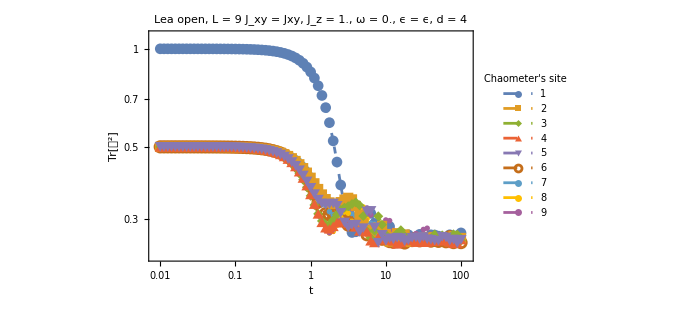

```mathematica
fig=ListLogLogPlot[Transpose[{t,#}]&/@choiPurities,
PlotRange->{{0.01-0.0015,120},{0.24-0.01,1+0.1}},
Joined->True,PlotStyle->Directive[Dashed],PlotMarkers->Automatic,
Frame->True,
FrameLabel->{HoldForm[TraditionalForm[t]],HoldForm[TraditionalForm[Tr[𝒟^2]]]},
FrameStyle->Directive[Black,FontSize->22],
FrameTicks->{{myTicksYLeft,myTicksYRight},{myTicksXBelow,myTicksXAbove}},
FrameTicksStyle->Directive[Black,20],
GridLines->{Table[10^i,{i,-2,2}],Range[0.25,1,0.05]},
ImageSize->500,
PlotLabel->"Lea open, "<>ToString[TraditionalForm[HoldForm[L]]]<>" = "<>ToString[L]<>"\n J_xy = "<>ToString[Jxy]<>", J_z = "<>ToString[Jz]<>", ω = "<>ToString[ω]<>", ϵ = "<>ToString[ϵ]<>", d = "<>ToString[defectsite],
LabelStyle->Directive[Black,FontSize->19],
ImagePadding->{{Automatic,Automatic},{Automatic,5}},
PlotLegends->LineLegend[ToString[#]&/@Range[9],LegendLabel->Placed["Chaometer's site",Above]]
]
```